```mathematica
getValues[function_, nodes_] := (
function/.x->nodes
)
getNodes[x0_,h_,n_] := (
Table[x0 + i*h, {i,0,n}]
)
newtonForward[n_,x0_,h_,f_] := (
nodes = getNodes[x0,h,n];
values = getValues[f,nodes];
p = (x-x0)/h;
product = 1;
forwardSum = 0;
For[i=0,i ≤  n,i++,
forwardSum += (findDiff[i,nodes,f]*product)/Factorial[i];
product *=(p-i);
];
forwardSum//Expand
)

findDiff[k_,nodes_,f_] := (
diff = 0;
For[j = 0,j≤k,j++,
diff+= (-1)^j*Factorial[k]/(Factorial[j]*Factorial[k-j])*(f/.x->nodes[[k-j+1]]);
];
diff//Expand
)
```

```mathematica
f[x_] = newtonForward[4,1,1,1/(25 +x^2)]
```

260447/6569225+(483 x)/525538-(321 x^2)/128180+(1113 x^3)/2627690-(613 x^4)/26276900

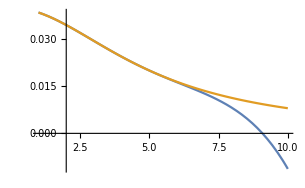

```mathematica
Plot[{f[x],1/(25 +x^2)},{x,1,10}]
```